```mathematica
(* HFAG, Combined Gs, DGs including correlated statistical and systemtatical uncertainties 
   Rick van Kooten, Olivier Leroy, update after ICHEP 2014 
  Don't forget to choose phis1 *)
```

DGsVersusGsSumer2016.pdf

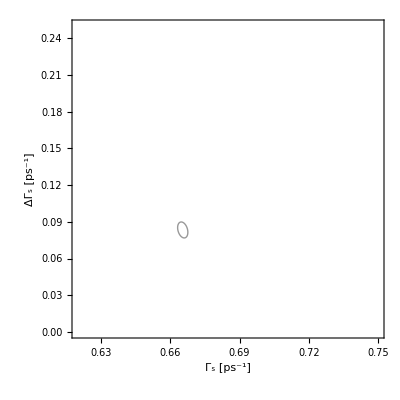

{xfit→0.665387,yfit→0.0833381,errxx→0.002216,erryy→0.00652212,rho→-0.292348}

-0.292348

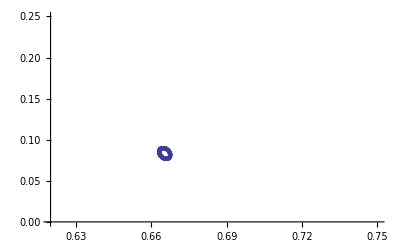

OutputStream[results_DGsGs_Summer2016.txt,74]

-Graphics-

-Graphics-

{xfit→0.664434,yfit→0.0859646,errxx→0.00213941,erryy→0.00609903,rho→-0.273149}

-0.273149

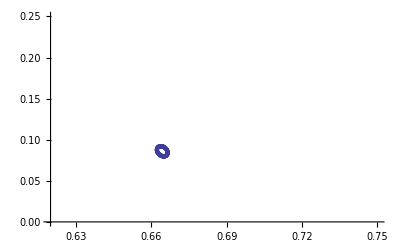

-Graphics-

{xfit→0.664522,yfit→0.0858173,errxx→0.00199538,erryy→0.00596153,rho→-0.216788}

-0.216788

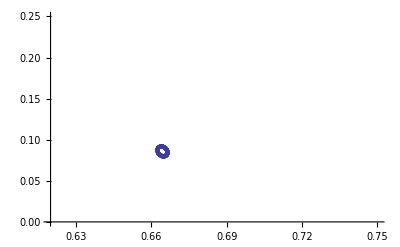

results_DGsGs_Summer2016.txt

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Helvetica,FontSize→18},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

FetchURL::httperr: The request to URL "http://marwww.in2p3.fr/~oleroy/pro/hfag/Sumer2016/hfag_logo_Sumer2016.pdf" was not successful. The server returned the HTTP status code "404 (\"Not Found\")".

$Failed

Show::gtype: Symbol is not a type of graphics.

-Graphics-

```mathematica
phis1 = 0.; 

Clear[f, g, h, pdfJpsihh, pdftot];

(* Plot ranges for Gs and DGs *)
Gsmin = 0.62;
Gsmax = 0.75;
DGsmin = 0;
DGsmax = 0.25;

(* First give JpsiPhi results for LHCb,ATLAS, CMS, CDF and D0. 
Then CP-even and CP-odd channels (e.g. Bs2KK and Bs2Jpsif0)
 Finally include the Flavour specific average  *)

(* LHCb inputs ================================================================================ *)
(* JpsiKK 3fb-1 *)

(* ONLY Jpsihh here,   Psi2SPhi is included later *)
myinput=ReadList["inputsHFAG_Summer2016.txt",Number]; (* All but Psi2SPhi *)
GsLHCb=myinput[[7]];
GsLHCbestat=myinput[[8]];
GsLHCbesyst=myinput[[9]];
GsLHCbetot = Sqrt[GsLHCbestat^2+GsLHCbesyst^2]; (* error tot *)

DGsLHCb=myinput[[4]];
DGsLHCbestat=myinput[[5]];
DGsLHCbesyst=myinput[[6]];

DGsLHCbetot = Sqrt[DGsLHCbestat^2+DGsLHCbesyst^2];


rhostaLHCb=-0.45; (* stat correl between Gs and DGs *)
rhosysLHCb = +0.44; (* sys correl between Gs and DGs *)
rhoLHCb = (GsLHCbestat*DGsLHCbestat*rhostaLHCb+GsLHCbesyst*DGsLHCbesyst*rhosysLHCb)/(GsLHCbetot*DGsLHCbetot); (* correl tot including stat and syst*)

(* now enter Psi2S LHCb run1 results *)
GsLHCbPsi2S=0.668;
GsLHCbPsi2Sestat=0.011;
GsLHCbPsi2Sesyst=0.006;
GsLHCbPsi2Setot = Sqrt[GsLHCbPsi2Sestat^2+GsLHCbPsi2Sesyst^2]; (* error tot *)

DGsLHCbPsi2S=0.066;
DGsLHCbPsi2Sestat=0.0425; (* symmetrize +0.041 - 0.044*)
DGsLHCbPsi2Sesyst=0.007;

DGsLHCbPsi2Setot = Sqrt[DGsLHCbPsi2Sestat^2+DGsLHCbPsi2Sesyst^2];


rhostaLHCbPsi2S=-0.40; (* stat correl between Gs and DGs *)
rhosysLHCbPsi2S = 0.; (* sys correl between Gs and DGs, assumed zero since not known *)
rhoLHCbPsi2S = (GsLHCbPsi2Sestat*DGsLHCbPsi2Sestat*rhostaLHCbPsi2S+GsLHCbPsi2Sesyst*DGsLHCbPsi2Sesyst*rhosysLHCbPsi2S)/(GsLHCbPsi2Setot*DGsLHCbPsi2Setot); 


(* ATLAS inputs ================================================================================ *)
(* atlas full run1, http://arxiv.org/abs/1601.03297 *)
GsATLAS = 0.675;
GsATLASestat =0.003;
GsATLASesyst = 0.003;
GsATLASetot = Sqrt[GsATLASestat^2+GsATLASesyst^2];

DGsATLAS = 0.085;
DGsATLASestat =  0.011;
DGsATLASesyst = 0.007;
DGsATLASetot = Sqrt[DGsATLASestat^2+DGsATLASesyst^2];

rhostaATLAS=-0.414; (* stat only *)
rhosysATLAS = 0;(* assume no correlated systematics between Gs and DGs *)
rhoATLAS = (GsATLASestat*DGsATLASestat*rhostaATLAS+GsATLASesyst*DGsATLASesyst*rhosysATLAS)/(GsATLASetot*DGsATLASetot); (* correl tot including stat and syst*)

(* CMS inputs ================================================================================ *)
(* published Phys.Lett.B 757,97 (2016), 20fb-1 8TeV only*)
clight=299.792458;
ctauCMS = 447.2;
ctauCMSestat = 2.9;
ctauCMSesyst = 3.7;
GsCMS = clight/ctauCMS;
(*clight=299792458.0e-6 taus_CMS= ctau/clight
taus_CMS_e=sqrt(0.00030**2+0.00035**2)/clight *)
GsCMSestat = clight*ctauCMSestat/(ctauCMS^2);
GsCMSesyst = clight*ctauCMSesyst/(ctauCMS^2);
GsCMSetot = Sqrt[GsCMSestat^2+GsCMSesyst^2];

DGsCMS = 0.095;
DGsCMSestat =  0.013;
DGsCMSesyst = 0.007;
DGsCMSetot = Sqrt[DGsCMSestat^2+DGsCMSesyst^2];

rhostaCMS=-0.55; (* rho(ctau,DGs)=+0.55, see summer2015/cms_phis_DGs_Gs_run1_EPS2015_Jack.pdf, Jack Cheng *)
(* rho(ctau,DGs) = rho(1/Gs,DGs) = -rho(Gs,DGs) *)
rhosysCMS = 0;(* assume no correlated systematics between Gs and DGs *)
rhoCMS = (GsCMSestat*DGsCMSestat*rhostaCMS+GsCMSesyst*DGsCMSesyst*rhosysCMS)/(GsCMSetot*DGsCMSetot); (* correl tot including stat and syst*)


(*CMS results with 4.9fb-1    => REMOVED at ICHEP 2016*)
GsCMS5=0.65456868558951964;
(*clight=299792458.0e-10 taus_CMS5=0.0458/clight taus_CMS5 _e=sqrt (0.00059**2+0.00022**2)/clight*)

GsCMS5estat=0.008432216692;
GsCMS5esyst=0.003144216393661448;
GsCMS5etot=Sqrt[GsCMS5estat^2+GsCMS5esyst^2];

DGsCMS5=0.048;
DGsCMS5estat=0.024;
DGsCMS5esyst=0.003;
DGsCMS5etot=Sqrt[DGsCMS5estat^2+DGsCMS5esyst^2];

rhostaCMS5=-0.673891;(*See april2013/CMS5_2012_MatrixCorrelation.pdf private Email from Kai-Feng Cheng*)rhosysCMS5=0;(*assume no correlated systematics between Gs and DGs*)rhoCMS5=(GsCMS5estat*DGsCMS5estat*rhostaCMS5+GsCMS5esyst*DGsCMS5esyst*rhosysCMS5)/(GsCMS5etot*DGsCMS5etot);
(*correl tot including stat and syst*)



(* CDF inputs ================================================================================ *)
GsCDF =0.65445026178;
(*tau=1.528 pm 0.019 (stat) pm 0.009 (syst) ps,Gs=1/tau=0.65445 pm 0.0081377977577 pm 0.0038547463  e_tau/tau**2 *)
GsCDFestat =0.0081377977577;
GsCDFesyst =0.0038547463;
GsCDFetot = Sqrt[GsCDFestat^2+GsCDFesyst^2];

DGsCDF = 0.068;
DGsCDFestat =  0.026;
DGsCDFesyst = 0.007;
DGsCDFetot = Sqrt[DGsCDFestat^2+DGsCDFesyst^2];

rhostaCDF=-0.52; (* -0.5 stat only *)
rhosysCDF = 0;(* assume no correlated systematics between Gs and DGs *)
rhoCDF = (GsCDFestat*DGsCDFestat*rhostaCDF+GsCDFesyst*DGsCDFesyst*rhosysCDF)/(GsCDFetot*DGsCDFetot); (* correl tot including stat and syst*)

(* D0 inputs ================================================================================ *)
GsD0 =0.6930;
(* taus=1.443+0.038-0.035=1.443 pm 0.0365 NO SYST GIVEN !*)
GsD0estat = 0.017529;
GsD0esyst =0.;
GsD0etot = Sqrt[GsD0estat^2+GsD0esyst^2];

DGsD0 = 0.163;
DGsD0estat =  0.0645;
DGsD0esyst = 0.0;
DGsD0etot = Sqrt[DGsD0estat^2+DGsD0esyst^2];

rhostaD0=-0.05; (* RickVK: http://www-d0.fnal.gov/Run2Physics/WWW/results/final/B/B11C/ *)
rhosysD0 =0;(* assume no correlated systematics between Gs and DGs *)
rhoD0 = (GsD0estat*DGsD0estat*rhostaD0+GsD0esyst*DGsD0esyst*rhosysD0)/(GsD0etot*DGsD0etot); (* correl tot including stat and syst*)


(* tauKK constraint, only LHCb.  tauKK = tauL(1+phis^2 ys/2 )*)
(* ol LHCb
tauKK1=1.45218;
etauKK1=0.04182; *)
(* new LHCb 2014 *)
tauKK1=1.407;
etauKK1 = 0.017464249;
CPeven = 1.;

(* tauL = tauKK/(1+phis^2*DGs/(4*Gs)); *)
(* effect of phis on tauL uncertainty is neglected! *)

(* tauDsDs constraint, only LHCb.  tauDsDs = tauL(1+phis^2 ys/2 )*)
tauDsDs1=1.37900;
etauDsDs1=0.03106;
CPeven = 1.;DGsVersusGsSumer2016.pdf

(* JpsiEta, LHCb ICHEP 2016, CP-even, tauL *)
tauJpsiEta1 = 1.479;
etauJpsiEta1 = 0.03573513677; (* sqrt(0.034**2+0.011**2) *)


(*tauJpsif0 constraint,only CDF. tauJpsif0=tauH(1-phis^2 ys/2)*)
(* average of CDF, LHCb JpsiPiPi 1fb-1 and D0 2016 *)
tauf01=1.65765;
etauf01 = 0.03188;(*symetrize the uncertainties : sqrt(.5*(.11**2+.12**2))=0.1151;sqrt(0.1151**2+0.03**2)*)
CPodd=-1.;
(* effect of phis on tauH uncertainty is neglected *)

(* tauJpsiKS constraint, only LHCb. tauJpsiKS = tauH(1-phis^2 ys/2)*)
tauJpsiKS1=1.75000;
etauJpsiKS1=0.13892;
CPodd = -1.;

(* Flavour specific lifetime 2014, including tauDsD from LHCb 
previous tau_FS=1.463 pm 0.032. New average spring 2014, including LHCb
tau_fs(DsD)=1.52 pm 0.15 pm 0.01 ps #=1.52 pm 0.15
=>tau_FS_2014=1.465 pm 0.031 # (1/sqrt(1/.15**2+1/.032**2))*(1.52/.15**2+1.463/.032**2)
*)

(* ichep2014, DsD, piK and DsPi + new D0 DsMuNu. Do not used Bs->piK penguin polluted *)
tauFS1 =1.516;
etauFS1 =0.014;




(* Now start the combination ============================================================= *)

(* Joint pdf of Gs and DGs for JpsiPhi-like channels *)
f[x_,y_,Gs_,eGs_,DGs_,eDGs_,rho_]:=1/(2*Pi*eGs*eDGs*Sqrt[1-rho^2])*Exp[(-1./(2*(1-rho^2)))*((x-Gs)^2/eGs^2 + (y-DGs)^2/eDGs^2- 2*rho*(x-Gs)*(y-DGs)/(eGs*eDGs))];

(* Named Jpsihh but also includes Psi2SPhi *)
pdfJpsihh[x_,y_]:=f[x,y,GsLHCb,GsLHCbetot,DGsLHCb,DGsLHCbetot,rhoLHCb]*f[x,y,GsLHCbPsi2S,GsLHCbPsi2Setot,DGsLHCbPsi2S,DGsLHCbPsi2Setot,rhoLHCbPsi2S]*
f[x,y,GsATLAS,GsATLASetot,DGsATLAS,DGsATLASetot,rhoATLAS]*
f[x,y,GsCDF,GsCDFetot,DGsCDF,DGsCDFetot,rhoCDF]*
f[x,y,GsCMS,GsCMSetot,DGsCMS,DGsCMSetot,rhoCMS]*
f[x,y,GsD0,GsD0etot,DGsD0,DGsD0etot,rhoD0] ;

(*pdfJpsihh[x_,y_]:=f[x,y,GsLHCb,GsLHCbetot,DGsLHCb,DGsLHCbetot,rhoLHCb]*f[x,y,GsLHCbPsi2S,GsLHCbPsi2Setot,DGsLHCbPsi2S,DGsLHCbPsi2Setot,rhoLHCbPsi2S]*
f[x,y,GsATLAS,GsATLASetot,DGsATLAS,DGsATLASetot,rhoATLAS]*
f[x,y,GsCDF,GsCDFetot,DGsCDF,DGsCDFetot,rhoCDF]*
f[x,y,GsCMS,GsCMSetot,DGsCMS,DGsCMSetot,rhoCMS]*f[x,y,GsCMS5,GsCMS5etot,DGsCMS5,DGsCMS5etot,rhoCMS5]*
f[x,y,GsD0,GsD0etot,DGsD0,DGsD0etot,rhoD0] ;  *)

(* Generic joint pdf of Gs and DGs for CP-eigenstate channels (Bs2KK, eta=+1, Jpsif0 eta=-1) *)
(* tauKK = tauL(1+phis^2 ys/2) ;    tauL = 2/(2G+DG)  *)
g[x_,y_,tauCP_,etauCP_, phis_, eta_]:=(1/(Sqrt[2*Pi]*etauCP))*Exp[(-1./2)*(  ( ( (2./(2x+eta*y))*(1+eta*phis^2*y/(4*x))-tauCP)/etauCP    )^2 )];

(* Joint pdf of Gs and DGs for flavour-specific lifetime tauFS = (1/Gs)*(1+ys^2)/(1-ys^2) *)
h[x_,y_,tauFS_,etauFS_]:=(1/(Sqrt[2*Pi]*etauFS))*Exp[(-1./2)*(  ( (   (1/x)*( 1+(y/(2*x))^2 )/(1-(y/(2*x))^2)   -tauFS)/etauFS    )^2 )];

(* total pdf, including JpsiKK, JpsiPipi, CP and flavour specific lifetimes *)

(*Dont use Bs2KK, penguin polluted *)
(*gCPeven[x_,y_]:=g[x,y,tauKK1,etauKK1, phis1, CPeven]*g[x,y,tauDsDs1,etauDsDs1, phis1, CPeven]; *)
gCPeven[x_,y_]:=g[x,y,tauDsDs1,etauDsDs1, phis1, CPeven]*
g[x,y,tauJpsiEta1,etauJpsiEta1, phis1, CPeven]; 

(*Dont use Bs2JpsiKS penguin polluted *)
(* gCPodd[x_,y_]:=g[x,y,tauf01,etauf01, phis1, CPodd]*g[x,y,tauJpsiKS1,etauJpsiKS1, phis1, CPodd]; *)
gCPodd[x_,y_]:=g[x,y,tauf01,etauf01, phis1, CPodd];


totpdf[x_,y_]:=pdfJpsihh[x,y]*gCPeven[x,y]*gCPodd[x,y]*h[x,y,tauFS1,etauFS1];



(* For illustration only, plot the pdf *)
(* Plot3D[f[x,y,GsLHCb,GsLHCbestat,DGsLHCb,DGsLHCbestat,rhoLHCb],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax}, Mesh->None, MaxRecursion->4,PlotRange->All] 

Plot3D[g[x,y,tauKK1,etauKK1, phis1, CPeven],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax}, Mesh->None, MaxRecursion->4,PlotRange->All]

Plot3D[g[x,y,tauf01,etauf01, phis1, CPodd],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax}, Mesh->None, MaxRecursion->4,PlotRange->All]

Plot3D[h[x,y,tauFS1,etauFS1],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax}, Mesh->None, MaxRecursion->4,PlotRange->All] *)

(* ###############################################################################  *)
(* Jpsihh ONLY*)
(* ###############################################################################  *)

min1 =FindMinValue[ -1*pdfJpsihh[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour1=-1.0*min1*Exp[-0.5];
myplot1 = ContourPlot[pdfJpsihh[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},Contours->{contour1},PlotPoints->150,PlotRange->Full, ContourShading->False,Axes->True, FrameLabel->{Style["Γ_s [ps^-1]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]}] 

xmin =x/.Last[FindMinimum[-1*pdfJpsihh[x,y],{x,Gsmin,Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]];
ymin = y/.Last[FindMinimum[-1*pdfJpsihh[x,y],{x,Gsmin,Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]]; 

points=Cases[Normal@myplot1,x_Line:>First@x,Infinity];
eplusGs=Max[points[[1]][[All,1]]]-xmin;
eminusGs = xmin-Min[points[[1]][[All,1]]];
eplusDGs = Max[points[[1]][[All,2]]]-ymin;
eminusDGs = ymin-Min[points[[1]][[All,2]]];

errGs=(eplusGs+eminusGs)/2;
errDGs=(eplusDGs+eminusDGs)/2;

(*Find correlation*)
(*get list of (x,y) coordinates*)
list2=First[points];
(*how many (x,y) points*)
veclen=Length[list2];
(*make a vector same length,filled with value of 1.0*)
vecones=Table[1.0,{i,veclen}];
(*effectively insert to each pair of (x,y) points,i.e.,(x,y,1.0),desired value of expression at (x,y)*)
fitlist=Transpose[Append[Transpose[list2],vecones]];
(*tilted error ellipse*)

ellipse=(xx-xfit)^2/errxx^2-2*rho*(xx-xfit)*(yy-yfit)/(errxx*erryy)+(yy-yfit)^2/erryy^2+rho^2;
(*fit to (x,y) points;use starting values determined above*)
fit=FindFit[fitlist,ellipse,{{xfit,xmin},{yfit,ymin},{errxx,errGs},{erryy,errDGs},{rho,0}},{xx,yy}]
rhocor=rho/.Last[fit]
ListPlot[points,PlotRange->{{Gsmin,Gsmax},{DGsmin,DGsmax}}]


str=OpenWrite["results_DGsGs_Summer2016.txt"]
WriteString[str,"Fit using ONLY Bs->Jpsihh : \n =========================================================================== \n"]
WriteString[str,"DGs = ", ymin, "^{+", eplusDGs , "} _{-", eminusDGs,"} \n"]
WriteString[str,"Gs = ", xmin, "^{+", eplusGs , "} _{-", eminusGs,"} \n"]
WriteString[str,"rho(Gs,DGs) = ",rhocor ,"\n"]
WriteString[str,"taus = 1/Gs = ", 1/xmin, "^{+", eplusGs/(xmin^2) , "} _{-", eminusGs/(xmin^2),"} \n"]

(* Transform to get GH, GL and DGs/Gs *)
tauL = 2/(2*xmin+ymin);
etauL=(2/(2 xmin+ymin)^2)*Sqrt[4 errGs^2+errDGs^2+4 rhocor*errGs *errDGs];

tauH = 2/(2*xmin-ymin);
etauH=(2/(2 xmin-ymin)^2)*Sqrt[(4 errGs^2+errDGs^2-4 rhocor*errGs*errDGs)];

DGsoverGs = ymin/xmin;
(* eDGsOvGs=Sqrt[(1/Gs)**2*eDGs**2+(DGs/Gs**2)**2*eGs**2+2*cor*eGs*eDGs*(1/Gs)*(-DGs/Gs**2)]; *)
eDGsOvGs=Sqrt[(1/xmin)^2*errDGs^2+(ymin/xmin^2)^2*errGs^2+2*rhocor*errGs*errDGs*(1/xmin)*(-ymin/xmin^2)];

(* need correl coeff of the combined result *)
WriteString[str,"tauL = 1/GL = ", tauL,"+/-", etauL,"\n"] 
WriteString[str,"tauH = 1/GH = ", tauH,"+/-", etauH,"\n"] 
WriteString[str,"DGs/Gs = ", DGsoverGs, "+/-", N[eDGsOvGs],"\n"] 

(*Close[str]*)


(* ###############################################################################  *)
(* Jpsihh + effective lifetime *)
(* ###############################################################################  *)

totpdf2[x_,y_]:=pdfJpsihh[x,y]*gCPeven[x,y]*gCPodd[x,y];

(* CP-even, tauKK, tauDsDs, tauL  *)
min2 =FindMinValue[ -1*gCPeven[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour2=-1.0*min2*Exp[-0.5];
myplot2 = ContourPlot[gCPeven[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},Contours->{contour2},PlotPoints->150,PlotRange->Full,ContourShading->{Transparent,LightPink},FrameLabel->{Style["Γ_s [ps^-1]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]}]

(* CP-odd, tauJpsif0, tauBs2JpsiKS, tauH  *)
min3 =FindMinValue[ -1*gCPodd[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour3=-1.0*min3*Exp[-0.5];
myplot3 = ContourPlot[gCPodd[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},Contours->{contour3},PlotPoints->150,PlotRange->Full,ContourShading->{Transparent,LightGreen},FrameLabel->{Style["Γ_s [ps^-1]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]}]

min =FindMinValue[ -1*totpdf2[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour=-1.0*min*Exp[-0.5];
myplot = ContourPlot[totpdf2[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},Contours->{contour},PlotPoints->150,PlotRange->Full,ContourShading->{Transparent,LightGray},FrameLabel->{Style["Γ_s [ps^-1]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]}];

xmin =x/.Last[FindMinimum[-1*totpdf2[x,y],{x,Gsmin,Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]];
ymin = y/.Last[FindMinimum[-1*totpdf2[x,y],{x,Gsmin,Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]]; 

points=Cases[Normal@myplot,x_Line:>First@x,Infinity];
eplusGs=Max[points[[1]][[All,1]]]-xmin;
eminusGs = xmin-Min[points[[1]][[All,1]]];
eplusDGs = Max[points[[1]][[All,2]]]-ymin;
eminusDGs = ymin-Min[points[[1]][[All,2]]];

errGs=(eplusGs+eminusGs)/2;
errDGs=(eplusDGs+eminusDGs)/2;

(*Find correlation*)
(*get list of (x,y) coordinates*)

list2=First[points];
(*how many (x,y) points*)
veclen=Length[list2];
(*make a vector same length,filled with value of 1.0*)

vecones=Table[1.0,{i,veclen}];
(*effectively insert to each pair of (x,y) points,i.e.,(x,y,1.0),desired value of expression at (x,y)*)

fitlist=Transpose[Append[Transpose[list2],vecones]];
(*tilted error ellipse*)

ellipse=(xx-xfit)^2/errxx^2-2*rho*(xx-xfit)*(yy-yfit)/(errxx*erryy)+(yy-yfit)^2/erryy^2+rho^2;
(*fit to (x,y) points;use starting values determined above*)
fit=FindFit[fitlist,ellipse,{{xfit,xmin},{yfit,ymin},{errxx,errGs},{erryy,errDGs},{rho,0}},{xx,yy}]
rhocor=rho/.Last[fit]
ListPlot[points,PlotRange->{{Gsmin,Gsmax},{DGsmin,DGsmax}}]


WriteString[str," \n"]
WriteString[str,"Fit using Jpsihh and effective lifetimes (CP-even and odd ) : \n =========================================================================== \n"]
WriteString[str,"DGs = ", ymin, "^{+", eplusDGs , "} _{-", eminusDGs,"} \n"]
WriteString[str,"Gs = ", xmin, "^{+", eplusGs , "} _{-", eminusGs,"} \n"]
WriteString[str,"rho(Gs,DGs) = ",rhocor ,"\n"]
WriteString[str,"taus = 1/Gs = ", 1/xmin, "^{+", eplusGs/(xmin^2) , "} _{-", eminusGs/(xmin^2),"} \n"]

(* Transform to get GH, GL and DGs/Gs *)
tauL = 2/(2*xmin+ymin);
etauL=(2/(2 xmin+ymin)^2)*Sqrt[4 errGs^2+errDGs^2+4 rhocor*errGs *errDGs];

tauH = 2/(2*xmin-ymin);
etauH=(2/(2 xmin-ymin)^2)*Sqrt[(4 errGs^2+errDGs^2-4 rhocor*errGs*errDGs)];

DGsoverGs = ymin/xmin;
(* eDGsOvGs=Sqrt[(1/Gs)**2*eDGs**2+(DGs/Gs**2)**2*eGs**2+2*cor*eGs*eDGs*(1/Gs)*(-DGs/Gs**2)]; *)
eDGsOvGs=Sqrt[(1/xmin)^2*errDGs^2+(ymin/xmin^2)^2*errGs^2+2*rhocor*errGs*errDGs*(1/xmin)*(-ymin/xmin^2)];

(* need correl coeff of the combined result *)
WriteString[str,"tauL = 1/GL = ", tauL,"+/-", etauL,"\n"] 
WriteString[str,"tauH = 1/GH = ", tauH,"+/-", etauH,"\n"] 
WriteString[str,"DGs/Gs = ", DGsoverGs, "+/-", N[eDGsOvGs],"\n"] 


(* ###############################################################################  *)
(* DEFAULT: Jpsihh + effective lifetime + flavour specific lifetime *)
(* ###############################################################################  *)
totpdf[x_,y_]:=pdfJpsihh[x,y]*gCPeven[x,y]*gCPodd[x,y]*h[x,y,tauFS1,etauFS1];

(* Flavour specific *)
min4 =FindMinValue[ -1*h[x,y,tauFS1,etauFS1],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour4=-1.0*min4*Exp[-0.5];
myplot4 = ContourPlot[h[x,y,tauFS1,etauFS1],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},Contours->{contour4},PlotPoints->150,PlotRange->Full,ContourShading->{Transparent,LightBlue},FrameLabel->{Style["Γ_s [ps^-1]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]}]

(* tot pdf *)
min =FindMinValue[ -1*totpdf[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]; 
contour=-1.0*min*Exp[-0.5];
myplot = ContourPlot[totpdf[x,y],{x,Gsmin, Gsmax},{y,DGsmin,DGsmax},Contours->{contour},PlotPoints->150,PlotRange->Full,ContourShading->{Transparent,LightGray},FrameLabel->{Style["Γ_s [ps^-1]",Bold,Black],Style["ΔΓ_s [ps^-1]",Bold,Black]}];

xmin =x/.Last[FindMinimum[-1*totpdf[x,y],{x,Gsmin,Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]];
ymin = y/.Last[FindMinimum[-1*totpdf[x,y],{x,Gsmin,Gsmax},{y,DGsmin,DGsmax},MaxIterations->100]]; 

points=Cases[Normal@myplot,x_Line:>First@x,Infinity];
eplusGs=Max[points[[1]][[All,1]]]-xmin;
eminusGs = xmin-Min[points[[1]][[All,1]]];
eplusDGs = Max[points[[1]][[All,2]]]-ymin;
eminusDGs = ymin-Min[points[[1]][[All,2]]];

errGs=(eplusGs+eminusGs)/2;
errDGs=(eplusDGs+eminusDGs)/2;

(*Find correlation*)
(*get list of (x,y) coordinates*)

list2=First[points];
(*how many (x,y) points*)
veclen=Length[list2];
(*make a vector same length,filled with value of 1.0*)

vecones=Table[1.0,{i,veclen}];
(*effectively insert to each pair of (x,y) points,i.e.,(x,y,1.0),desired value of expression at (x,y)*)

fitlist=Transpose[Append[Transpose[list2],vecones]];
(*tilted error ellipse*)

ellipse=(xx-xfit)^2/errxx^2-2*rho*(xx-xfit)*(yy-yfit)/(errxx*erryy)+(yy-yfit)^2/erryy^2+rho^2;
(*fit to (x,y) points;use starting values determined above*)
fit=FindFit[fitlist,ellipse,{{xfit,xmin},{yfit,ymin},{errxx,errGs},{erryy,errDGs},{rho,0}},{xx,yy}]
rhocor=rho/.Last[fit]
ListPlot[points,PlotRange->{{Gsmin,Gsmax},{DGsmin,DGsmax}}]

WriteString[str," \n"]
WriteString[str,"DEFAULT fit using Jpsihh, effective lifetimes and tauFS : \n =========================================================================== \n"]
WriteString[str,"DGs = ", ymin, "^{+", eplusDGs , "} _{-", eminusDGs,"} \n"]
WriteString[str,"Gs = ", xmin, "^{+", eplusGs , "} _{-", eminusGs,"} \n"]
WriteString[str,"rho(Gs,DGs) = ",rhocor ,"\n"]
WriteString[str,"taus = 1/Gs = ", 1/xmin, "^{+", eplusGs/(xmin^2) , "} _{-", eminusGs/(xmin^2),"} \n"]

(* Transform to get GH, GL and DGs/Gs *)
tauL = 2/(2*xmin+ymin);
etauL=(2/(2 xmin+ymin)^2)*Sqrt[4 errGs^2+errDGs^2+4 rhocor*errGs *errDGs];

tauH = 2/(2*xmin-ymin);
etauH=(2/(2 xmin-ymin)^2)*Sqrt[(4 errGs^2+errDGs^2-4 rhocor*errGs*errDGs)];

DGsoverGs = ymin/xmin;
(* eDGsOvGs=Sqrt[(1/Gs)**2*eDGs**2+(DGs/Gs**2)**2*eGs**2+2*cor*eGs*eDGs*(1/Gs)*(-DGs/Gs**2)]; *)
eDGsOvGs=Sqrt[(1/xmin)^2*errDGs^2+(ymin/xmin^2)^2*errGs^2+2*rhocor*errGs*errDGs*(1/xmin)*(-ymin/xmin^2)];

(* need correl coeff of the combined result *)
WriteString[str,"tauL = 1/GL = ", tauL,"+/-", etauL,"\n"] 
WriteString[str,"tauH = 1/GH = ", tauH,"+/-", etauH,"\n"] 
WriteString[str,"DGs/Gs = ", DGsoverGs, "+/-", N[eDGsOvGs],"\n"] 

(*WriteString[str, "\n Combined CP-even modes \n ========================================= \n "]
etauLa = 1/Sqrt[1./etauKK1^2+1/etauDsDs1^2];
tauLa = etauLa^2*(tauKK1/etauKK1^2+tauDsDs1/etauDsDs1^2);
 WriteString[str,"tauL (KK and DsDs) = ", tauLa,"+/-", etauLa,"\n"];

WriteString[str, "\n Combined CP-odd modes \n ========================================= \n "]
etauHa = 1/Sqrt[1./etauf01^2+1/etauJpsiKS1^2]
tauHa = etauHa^2*(tauf01/etauf01^2+tauJpsiKS1/etauJpsiKS1^2)
 WriteString[str,"tauH (Jpsif0 and JpsiKS) = ", tauHa,"+/-", etauHa,"\n"]; *)

Close[str]

(*Default font options on the contour plots*)
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->18}]

g=Import["http://marwww.in2p3.fr/~oleroy/pro/hfag/Sumer2016/hfag_logo_Sumer2016.pdf"]
finalPlot=Show[myplot4,myplot2,myplot3,myplot,myplot1,BaseStyle->{FontWeight->"Bold",FontSize->15},ImageSize->{600,600},AspectRatio->Full,Epilog->{Text[Style["68% CL regions",21],{1.1,0.16}],
Text[Style["Flavour Specific",20,Blue],{0.67,0.24}],
Text[Style["ccKK",20,Black],{0.65,0.073}],
Text[Style["Combined",20,Black],{0.68,0.09}],
Text[Style["J/ψππ+J/ψf_0",20,Green],{0.72,0.17}],
Text[Style["DsDs+J/ψη",20,Red],{0.73,0.06}],
Inset[Show[g],{0.74,0.24}]
}]

Export["DGsVersusGsSummer2016.pdf",finalPlot];
Export["DGsVersusGsSummer2016.jpg",finalPlot];
Export["DGsVersusGsSummer2016.gif",finalPlot];
```